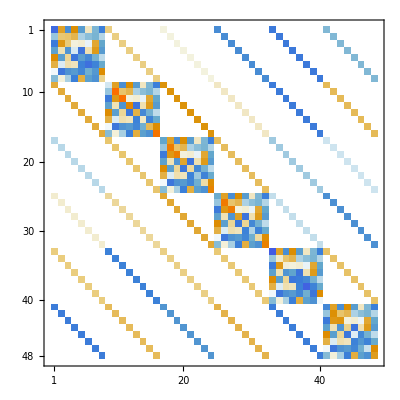

1.16579×10^-15

```mathematica
{m,n}={6,8};
X=RandomReal[{-1,1},{m,n}];
A=RandomReal[{-1,1},{m,m}];
B=RandomReal[{-1,1},{n,n}];
CMat=A.X+X.B;
M=KroneckerProduct[A,IdentityMatrix[n]]+KroneckerProduct[IdentityMatrix[m],Bᵀ];
MatrixPlot[M]
Norm[A.X+X.B - Partition[M.Flatten[X],n]]
```